# FileAdapterGSDGSH test

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

(last updated:  Thu 27 Feb 2014 23:31:35)

<<Set JLink` java stack size to 3072Mb>>

```mathematica
ShowJavaConsole[];
```

```mathematica
testDataFile = "V:\\docs\\bb\\nounous\\src\\test\\resources\\_testFiles\\Micam\\mag130712008A_3.gsd";
```

```mathematica
$NNReader@load[testDataFile]
```

```mathematica
$NNReader@toStringChain[]
```

DataReader LOADED DATA SUMMARY
================================
DataReader( data ch:7360, dataAux ch:2, layout: XLayoutNull, mask: XMask: 0 _masks, events: 0)

     [header  ] XHeader: 26 entries
     [dataORI ] XDataFilterHolder: XData: 7360 ch, 1 seg, lengths=Vector(1025), fs=500.0)     
          \ XDataFilterDecimate: off (factor=1)     
               \ XDataFilterBuffer: bufferPageLength=16384, garbageQueBound=1024     
                    \ XDataFilterStatistics: 
                    \ XDataFilterMinMaxAbs: halfWindow=25
                    \ XDataFilterFIR: kernel null (off)     
                         \ XDataFilterRMS: halfWindow=25
                    \ XDataFilterFIR: kernel null (off)
     [dataAux ] XDataFilterHolder: XData: 2 ch, 1 seg, lengths=Vector(1024), fs=500.0)
     [layout  ] XLayoutNull
     [mask    ] XMask: 0 _masks
     [events  ] XEventsNull
     [spikes  ] XSpikesNull

```mathematica
$NNReader@dataFIR[]@segmentLengths[]@toString[]
```

Vector(1025)

```mathematica
$NNReader@dataDecimate[]@segmentLengths[]@toString[]
```

Vector(1025)

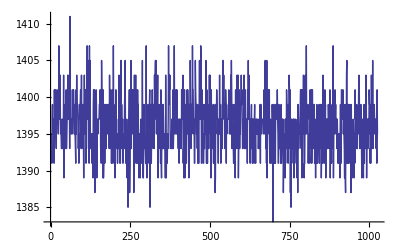

```mathematica
ListLinePlot[$NNReader@dataFIR[]@readTraceAbsA[100, NN`frAll[]]]
```

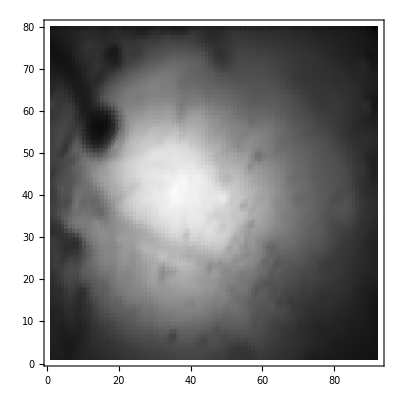

```mathematica
ListDensityPlot[Partition[$NNReader@dataFIR[]@readFrameA[0,0],92],ColorFunction->GrayLevel]
```